```mathematica
basis=N[{{0,0},{1/2,Sqrt[3]/2},{1,0},{1/2 (1+Sqrt[3]),1/2 (1+Sqrt[3])},{1/2 (2+Sqrt[3]),1/2},{1/2 (3+Sqrt[3]),1/2 (1+Sqrt[3])}}]
a2=N[(√3+1){1/2,√3/2}];
a1=N[(√3+1){1,0}];
l=12;
sites=Flatten[Table[a1*i+basis[[k]],{i,1,l},{k,1,6}],1]
If[OddQ[l],
sites=Delete[sites,{{6*l-2},{6*l-1},{6*l}}]]
n=Length[sites]
```

{{0.,0.},{0.5,0.866025},{1.,0.},{1.36603,1.36603},{1.86603,0.5},{2.36603,1.36603}}

{{2.73205,0.},{3.23205,0.866025},{3.73205,0.},{4.09808,1.36603},{4.59808,0.5},{5.09808,1.36603},{5.4641,0.},{5.9641,0.866025},{6.4641,0.},{6.83013,1.36603},{7.33013,0.5},{7.83013,1.36603},{8.19615,0.},{8.69615,0.866025},{9.19615,0.},{9.56218,1.36603},{10.0622,0.5},{10.5622,1.36603},{10.9282,0.},{11.4282,0.866025},{11.9282,0.},{12.2942,1.36603},{12.7942,0.5},{13.2942,1.36603},{13.6603,0.},{14.1603,0.866025},{14.6603,0.},{15.0263,1.36603},{15.5263,0.5},{16.0263,1.36603},{16.3923,0.},{16.8923,0.866025},{17.3923,0.},{17.7583,1.36603},{18.2583,0.5},{18.7583,1.36603},{19.1244,0.},{19.6244,0.866025},{20.1244,0.},{20.4904,1.36603},{20.9904,0.5},{21.4904,1.36603},{21.8564,0.},{22.3564,0.866025},{22.8564,0.},{23.2224,1.36603},{23.7224,0.5},{24.2224,1.36603},{24.5885,0.},{25.0885,0.866025},{25.5885,0.},{25.9545,1.36603},{26.4545,0.5},{26.9545,1.36603},{27.3205,0.},{27.8205,0.866025},{28.3205,0.},{28.6865,1.36603},{29.1865,0.5},{29.6865,1.36603},{30.0526,0.},{30.5526,0.866025},{31.0526,0.},{31.4186,1.36603},{31.9186,0.5},{32.4186,1.36603},{32.7846,0.},{33.2846,0.866025},{33.7846,0.},{34.1506,1.36603},{34.6506,0.5},{35.1506,1.36603}}

72

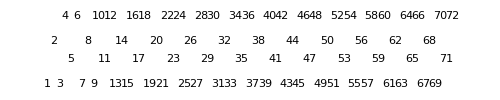

```mathematica
it=Graphics[{Table[{White,EdgeForm[Thick],Disk[sites[[i]],0.15]},{i,1,Length[sites]}],Table[{Text[i,sites[[i]]]},{i,1,Length[sites]}]},ImageSize->500]
```

```mathematica
nnJ12={};nnJ8={};nnJ11={};nnJ3={};nnJ7={};nnJ5={};nnJ10={};nnJ4={};nnJ2={};nnJ9={};
Do[Do[{If[(Simplify[Norm[sites[[i]]-sites[[j]]]]==1&&Mod[i,6]==1&&Mod[j,6]==2),AppendTo[nnJ12,{j,i}]],
If[(Simplify[Norm[sites[[i]]-sites[[j]]]]==1&&Mod[i,6]==1&&Mod[j,6]==3),AppendTo[nnJ8,{j,i}]],
If[(Simplify[Norm[sites[[i]]-sites[[j]]]]==1&&Mod[i,6]==2&&Mod[j,6]==3),AppendTo[nnJ11,{j,i}]],
If[(Simplify[Norm[sites[[i]]-sites[[j]]]]==1&&Mod[i,6]==2&&Mod[j,6]==4),AppendTo[nnJ3,{j,i}]],
If[(Simplify[Norm[sites[[i]]-sites[[j]]]]==1&&Mod[i,6]==3&&Mod[j,6]==5),AppendTo[nnJ7,{j,i}]],
If[(Simplify[Norm[sites[[i]]-sites[[j]]]]==1&&Mod[i,6]==4&&Mod[j,6]==5),AppendTo[nnJ5,{j,i}]],
If[(Simplify[Norm[sites[[i]]-sites[[j]]]]==1&&Mod[i,6]==4&&Mod[j,6]==0),AppendTo[nnJ10,{j,i}]],
If[(Simplify[Norm[sites[[i]]-sites[[j]]]]==1&&Mod[i,6]==5&&Mod[j,6]==0),AppendTo[nnJ4,{j,i}]],
If[(Simplify[Norm[sites[[i]]-sites[[j]]]]==1&&Mod[i,6]==0&&Mod[j,6]==2),AppendTo[nnJ2,{j,i}]],
If[(Simplify[Norm[sites[[i]]-sites[[j]]]]==1&&Mod[i,6]==5&&Mod[j,6]==1),AppendTo[nnJ9,{j,i}]],
},{j,i,Length[sites]}],{i,1,Length[sites]}];
```

```mathematica
cp=Reverse[ResourceFunction["ColorBrewerData"]["Set1",12]]
```

FunctionRepository`$cb2edf2c655749de9e1c90cb79dff58a`ColorBrewerData::interpolatecolorscheme: Color scheme Set1 has at most 9 colors, interpolating will be used to get 12 colors.

{RGBColor[Rational[3, 5], Rational[3, 5], Rational[3, 5]],RGBColor[Rational[487, 561], Rational[497, 935], Rational[1987, 2805]],RGBColor[Rational[136, 165], Rational[1204, 2805], Rational[1346, 2805]],RGBColor[Rational[668, 935], Rational[428, 935], Rational[14, 85]],RGBColor[Rational[2716, 2805], Rational[2636, 2805], Rational[10, 51]],RGBColor[1, Rational[1909, 2805], Rational[4, 55]],RGBColor[Rational[2393, 2805], Rational[1201, 2805], Rational[652, 2805]],RGBColor[Rational[1597, 2805], Rational[191, 561], Rational[568, 935]],RGBColor[Rational[997, 2805], Rational[577, 935], Rational[992, 2805]],RGBColor[Rational[13, 51], Rational[1631, 2805], Rational[134, 255]],RGBColor[Rational[1124, 2805], Rational[362, 935], Rational[1556, 2805]],RGBColor[Rational[76, 85], Rational[26, 255], Rational[28, 255]]}

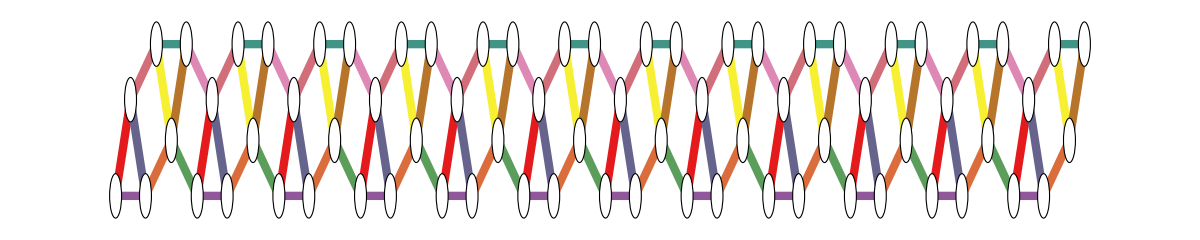

```mathematica
it1=Graphics[Table[{White,EdgeForm[{Black,Thick}],Disk[sites[[i]],0.2]},{i,1,Length[sites]}],ImageSize->1000];
iJ12=Graphics[Table[{cp[[12]],CapForm["Round"],Thickness[0.005],Arrowheads->0.02,Line[{sites[[nnJ12[[i,1]]]],sites[[nnJ12[[i,2]]]]}]},{i,Length[nnJ12]}]];
iJ8=Graphics[Table[{cp[[8]],CapForm["Round"],Thickness[0.005],Arrowheads->0.02,Line[{sites[[nnJ8[[i,1]]]],sites[[nnJ8[[i,2]]]]}]},{i,Length[nnJ8]}]];
iJ11=Graphics[Table[{cp[[11]],CapForm["Round"],Thickness[0.005],Arrowheads->0.02,Line[{sites[[nnJ11[[i,1]]]],sites[[nnJ11[[i,2]]]]}]},{i,Length[nnJ11]}]];
iJ3=Graphics[Table[{cp[[3]],CapForm["Round"],Thickness[0.005],Arrowheads->0.02,Line[{sites[[nnJ3[[i,1]]]],sites[[nnJ3[[i,2]]]]}]},{i,Length[nnJ3]}]];
iJ7=Graphics[Table[{cp[[7]],CapForm["Round"],Thickness[0.005],Arrowheads->0.02,Line[{sites[[nnJ7[[i,1]]]],sites[[nnJ7[[i,2]]]]}]},{i,Length[nnJ7]}]];
iJ5=Graphics[Table[{cp[[5]],CapForm["Round"],Thickness[0.005],Arrowheads->0.02,Line[{sites[[nnJ5[[i,1]]]],sites[[nnJ5[[i,2]]]]}]},{i,Length[nnJ5]}]];
iJ10=Graphics[Table[{cp[[10]],CapForm["Round"],Thickness[0.005],Arrowheads->0.02,Line[{sites[[nnJ10[[i,1]]]],sites[[nnJ10[[i,2]]]]}]},{i,Length[nnJ10]}]];
iJ4=Graphics[Table[{cp[[4]],CapForm["Round"],Thickness[0.005],Arrowheads->0.02,Line[{sites[[nnJ4[[i,1]]]],sites[[nnJ4[[i,2]]]]}]},{i,Length[nnJ4]}]];
iJ2=Graphics[Table[{cp[[2]],CapForm["Round"],Thickness[0.005],Arrowheads->0.02,Line[{sites[[nnJ2[[i,1]]]],sites[[nnJ2[[i,2]]]]}]},{i,Length[nnJ2]}]];
iJ9=Graphics[Table[{cp[[9]],CapForm["Round"],Thickness[0.005],Arrowheads->0.02,Line[{sites[[nnJ9[[i,1]]]],sites[[nnJ9[[i,2]]]]}]},{i,Length[nnJ9]}]];
im=Show[{iJ12,iJ8,iJ11,iJ3,iJ7,iJ5,iJ10,iJ4,iJ2,iJ9,it1},ImageSize->1200]
```

```mathematica
J1=5.59199/87.8909
J2=59.4077/87.8909
J3=9.19959/87.8909
J4=57.9561/87.8909
J5=32.8277/87.8909
J6=1.21387/87.8909
J7=76.6443/87.8909
J8=54.087/87.8909
J9=81.0975/87.8909
J10=87.8909/87.8909
J11=11.7514/87.8909
J12=26.6279/87.8909
```

0.0636242

0.675925

0.104671

0.65941

0.373505

0.0138111

0.872039

0.615388

0.922706

1.

0.133704

0.302965

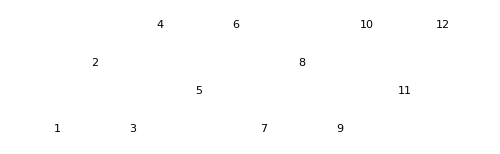

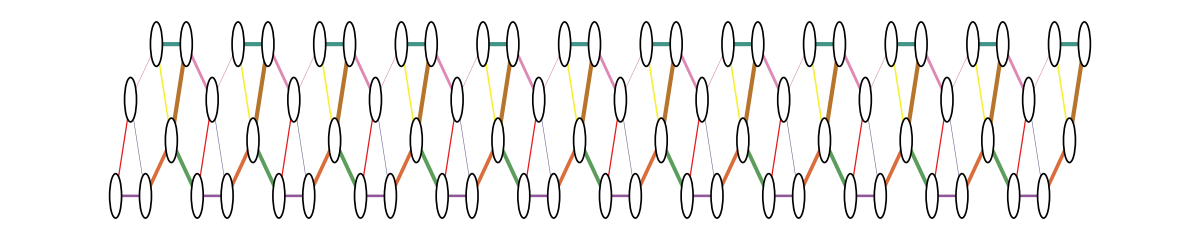

```mathematica
it1=Graphics[Table[{White,EdgeForm[{Black,Thickness[0.001]}],Disk[sites[[i]],0.2]},{i,1,Length[sites]}],ImageSize->1000];
iJ12=Graphics[Table[{cp[[12]],CapForm["Round"],Thickness[0.0025*J12],Arrowheads->0.02,Line[{sites[[nnJ12[[i,1]]]],sites[[nnJ12[[i,2]]]]}]},{i,Length[nnJ12]}]];
iJ8=Graphics[Table[{cp[[8]],CapForm["Round"],Thickness[0.0025*J8],Arrowheads->0.02,Line[{sites[[nnJ8[[i,1]]]],sites[[nnJ8[[i,2]]]]}]},{i,Length[nnJ8]}]];
iJ11=Graphics[Table[{cp[[11]],CapForm["Round"],Thickness[0.0025*J11],Arrowheads->0.02,Line[{sites[[nnJ11[[i,1]]]],sites[[nnJ11[[i,2]]]]}]},{i,Length[nnJ11]}]];
iJ3=Graphics[Table[{cp[[3]],CapForm["Round"],Thickness[0.0025*J3],Arrowheads->0.02,Line[{sites[[nnJ3[[i,1]]]],sites[[nnJ3[[i,2]]]]}]},{i,Length[nnJ3]}]];
iJ7=Graphics[Table[{cp[[7]],CapForm["Round"],Thickness[0.0025*J7],Arrowheads->0.02,Line[{sites[[nnJ7[[i,1]]]],sites[[nnJ7[[i,2]]]]}]},{i,Length[nnJ7]}]];
iJ5=Graphics[Table[{cp[[5]],CapForm["Round"],Thickness[0.0025*J5],Arrowheads->0.02,Line[{sites[[nnJ5[[i,1]]]],sites[[nnJ5[[i,2]]]]}]},{i,Length[nnJ5]}]];
iJ10=Graphics[Table[{cp[[10]],CapForm["Round"],Thickness[0.0025*J10],Arrowheads->0.02,Line[{sites[[nnJ10[[i,1]]]],sites[[nnJ10[[i,2]]]]}]},{i,Length[nnJ10]}]];
iJ4=Graphics[Table[{cp[[4]],CapForm["Round"],Thickness[0.0025*J10],Arrowheads->0.02,Line[{sites[[nnJ4[[i,1]]]],sites[[nnJ4[[i,2]]]]}]},{i,Length[nnJ4]}]];
iJ2=Graphics[Table[{cp[[2]],CapForm["Round"],Thickness[0.0025*J2],Arrowheads->0.02,Line[{sites[[nnJ2[[i,1]]]],sites[[nnJ2[[i,2]]]]}]},{i,Length[nnJ2]}]];
iJ9=Graphics[Table[{cp[[9]],CapForm["Round"],Thickness[0.0025*J9],Arrowheads->0.02,Line[{sites[[nnJ9[[i,1]]]],sites[[nnJ9[[i,2]]]]}]},{i,Length[nnJ9]}]];
im=Show[{iJ12,iJ8,iJ11,iJ3,iJ7,iJ5,iJ10,iJ4,iJ2,iJ9,it1},ImageSize->1200]
```

```mathematica
Export["/Users/pghosh/Work/Work2026/Ruby_CsBaTi3F12/Figs/1D_lattice.svg",im]
```

/Users/pghosh/Work/Work2026/Ruby_CsBaTi3F12/Figs/1D_lattice.svg

```mathematica
nn={};
Do[Do[{If[(Simplify[Norm[sites[[i]]-sites[[j]]]]==1&&Mod[i,6]==1&&Mod[j,6]==2),AppendTo[nn,{j,i,J12,J12}]],
If[(Simplify[Norm[sites[[i]]-sites[[j]]]]==1&&Mod[i,6]==1&&Mod[j,6]==3),AppendTo[nn,{j,i,J8,J8}]],
If[(Simplify[Norm[sites[[i]]-sites[[j]]]]==1&&Mod[i,6]==2&&Mod[j,6]==3),AppendTo[nn,{j,i,J11,J11}]],
If[(Simplify[Norm[sites[[i]]-sites[[j]]]]==1&&Mod[i,6]==2&&Mod[j,6]==4),AppendTo[nn,{j,i,J3,J3}]],
If[(Simplify[Norm[sites[[i]]-sites[[j]]]]==1&&Mod[i,6]==3&&Mod[j,6]==5),AppendTo[nn,{j,i,J7,J7}]],
If[(Simplify[Norm[sites[[i]]-sites[[j]]]]==1&&Mod[i,6]==4&&Mod[j,6]==5),AppendTo[nn,{j,i,J5,J5}]],
If[(Simplify[Norm[sites[[i]]-sites[[j]]]]==1&&Mod[i,6]==4&&Mod[j,6]==0),AppendTo[nn,{j,i,J10,J10}]],
If[(Simplify[Norm[sites[[i]]-sites[[j]]]]==1&&Mod[i,6]==5&&Mod[j,6]==0),AppendTo[nn,{j,i,J4,J4}]],
If[(Simplify[Norm[sites[[i]]-sites[[j]]]]==1&&Mod[i,6]==0&&Mod[j,6]==2),AppendTo[nn,{j,i,J2,J2}]],
If[(Simplify[Norm[sites[[i]]-sites[[j]]]]==1&&Mod[i,6]==5&&Mod[j,6]==1),AppendTo[nn,{j,i,J9,J9}]],
},{j,i,Length[sites]}],{i,1,Length[sites]}];
```

```mathematica
Export["/Users/pghosh/Work/Github/DSSF/sites_compound.dat",sites]
```

/Users/pghosh/Work/Github/DSSF/sites_compound.dat

```mathematica
Export["/Users/pghosh/Work/Github/DSSF/bonds_compound.dat",nn]
```

/Users/pghosh/Work/Github/DSSF/bonds_compound.dat